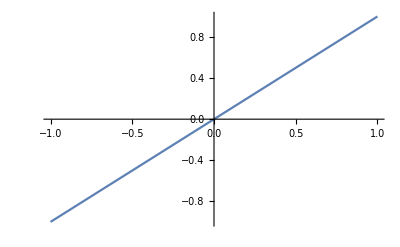

```mathematica
Plot[x,{x,-1,1}]
```

```mathematica
{x,x}.RotationMatrix[θ]
```

{x Cos[θ]+x Sin[θ],x Cos[θ]-x Sin[θ]}

```mathematica
Manipulate[
ParametricPlot[
{x,x}.RotationMatrix[θ]
,{x,0,1}]
,{θ,0,2π}]
```

```mathematica
Manipulate[
ParametricPlot[
{x,x}.RotationMatrix[θ]
,{x,0,1},PlotRange->{{-1,1},{-1,1}}]
,{θ,0,2π}]
```

```mathematica
Manipulate[
ParametricPlot[
Normalize[{x,x}.RotationMatrix[θ]]
,{x,0,1},PlotRange->{{-1,1},{-1,1}}]
,{θ,0,2π}]
```

```mathematica
Manipulate[
ParametricPlot[{
Normalize[{x,x}.RotationMatrix[θ]],
Normalize[{x,x}].Normalize[RotationMatrix[θ]]
},{x,0,1},PlotRange->{{-1,1},{-1,1}}]
,{θ,0,2π}]
```

Normalize::nlnmt2: The first argument is not a number or a vector, or the second argument is not a norm function that always returns a non-negative real number for any numeric argument.

General::stop: Further output of Normalize::nlnmt2 will be suppressed during this calculation.

Normalize::nlnmt2: The first argument is not a number or a vector, or the second argument is not a norm function that always returns a non-negative real number for any numeric argument.

General::stop: Further output of Normalize::nlnmt2 will be suppressed during this calculation.

```mathematica
Total@Map[Ceiling[Log[2,#]]&,Range@10]
```

25

```mathematica
Quantity[Total@Map[Ceiling[Log[2,#]]&,Range@10],"Bytes"]
```

25 B

```mathematica
Quantity[Total@Map[Ceiling[Log[2,#]]&,Differences@Range@10],"Bytes"]
```

0 B

```mathematica
Total@Map[Ceiling[Log[2,#]]&,Differences@Range@10]
```

0

```mathematica
Differences@Range@10
```

{1,1,1,1,1,1,1,1,1}

```mathematica
Ceiling[Log[2,1]]
```

0

```mathematica
RandomInteger[10]
```

8

```mathematica
RandomInteger[10,20]
```

{9,6,5,5,1,6,1,2,8,4,7,6,5,10,9,9,2,2,6,0}

```mathematica
Total@Map[Ceiling[Log[2,#]]&,Out[14]]
```

-∞

```mathematica
Differences@Out[14]
```

{-3,-1,0,-4,5,-5,1,6,-4,3,-1,-1,5,-1,0,-7,0,4,-6}

```mathematica
Manipulate[
ParametricPlot[{
Normalize[{x,x}.RotationMatrix[θ]],
Normalize[{x,x}.RotationMatrix[θ]].Normalize[{x,x}]
},{x,0,1},PlotRange->{{-1,1},{-1,1}}]
,{θ,0,2π}]
```

```mathematica
Manipulate[
ParametricPlot[{
Normalize[{x,x}.RotationMatrix[θ]],
Normalize[{x,x}.RotationMatrix[θ]].Normalize[{1,1}]
},{x,0,1},PlotRange->{{-1,1},{-1,1}}]
,{θ,0,2π}]
```

```mathematica
Normalize[{x,x}.RotationMatrix[θ]].Normalize[{1,1}]
```

(x Cos[θ]-x Sin[θ])/(√2 √(Abs[x Cos[θ]-x Sin[θ]]^2+Abs[x Cos[θ]+x Sin[θ]]^2))+(x Cos[θ]+x Sin[θ])/(√2 √(Abs[x Cos[θ]-x Sin[θ]]^2+Abs[x Cos[θ]+x Sin[θ]]^2))

```mathematica
FullSimplify[
Normalize[{x,x}.RotationMatrix[θ]].Normalize[{1,1}]
,{x,θ}∈Reals]
```

Cos[θ] Sign[x]

```mathematica
Manipulate[Plot[Cos[θ] Sign[x],{x,-10.,10.}],{θ,-6.283185307179586,6.283185307179586}]
```

```mathematica
Manipulate[Plot[Cos[θ] Sign[x],{x,-10.,10.}],{θ,-6.283185307179586,6.283185307179586}]
```

```mathematica
FullSimplify[
RotationMatrix[θ].Normalize[{1,1}]
,{x,θ}∈Reals]
```

{(Cos[θ]-Sin[θ])/(√2),(Cos[θ]+Sin[θ])/(√2)}

```mathematica
FullSimplify[
RotationMatrix[θ].Normalize[{1,1}]
,θ∈Reals]
```

{(Cos[θ]-Sin[θ])/(√2),(Cos[θ]+Sin[θ])/(√2)}

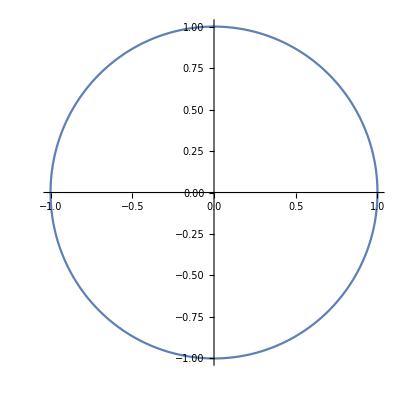

```mathematica
ParametricPlot[
{(Cos[θ]-Sin[θ])/(√2),(Cos[θ]+Sin[θ])/(√2)}
,{θ,0,2π}]
```

```mathematica
Solve[(Cos[θ]-Sin[θ])/(√2)==a,θ,Reals]
```

{{θ→ConditionalExpression[π/4-ArcSin[a]-2 π C[1],C[1]∈ℤ&&-1≤a≤1]},{θ→ConditionalExpression[-(3 π)/4+ArcSin[a]-2 π C[1],C[1]∈ℤ&&-1≤a≤1]}}

```mathematica
Normalize[{1,1}]
```

```mathematica
Normalize[D[{x,f[x]},x]]
```

{1/(√(1+Abs[f'[x]]^2)),f'[x]/(√(1+Abs[f'[x]]^2))}

```mathematica
FullSimplify[
Normalize[D[{x,f[x]},x]]
,x∈Reals]
```

{1/(√(1+Abs[f'[x]]^2)),f'[x]/(√(1+Abs[f'[x]]^2))}

```mathematica
FullSimplify[
Normalize[D[{x,f[x]},x]]
,{x,f[x],f'[x]}∈Reals]
```

{1/(√(1+f'[x]^2)),f'[x]/(√(1+f'[x]^2))}

```mathematica
{1/(√(1+f'[x]^2)),f'[x]/(√(1+f'[x]^2))}.RotationMatrix[θ]
```

{Cos[θ]/(√(1+f'[x]^2))+(Sin[θ] f'[x])/(√(1+f'[x]^2)),-Sin[θ]/(√(1+f'[x]^2))+(Cos[θ] f'[x])/(√(1+f'[x]^2))}

```mathematica
With[{f=Function[x,x^2]},
{Cos[θ]/(√(1+f'[x]^2))+(Sin[θ] f'[x])/(√(1+f'[x]^2)),-Sin[θ]/(√(1+f'[x]^2))+(Cos[θ] f'[x])/(√(1+f'[x]^2))}
]
```

{Cos[θ]/(√(1+4 x^2))+(2 x Sin[θ])/(√(1+4 x^2)),(2 x Cos[θ])/(√(1+4 x^2))-Sin[θ]/(√(1+4 x^2))}

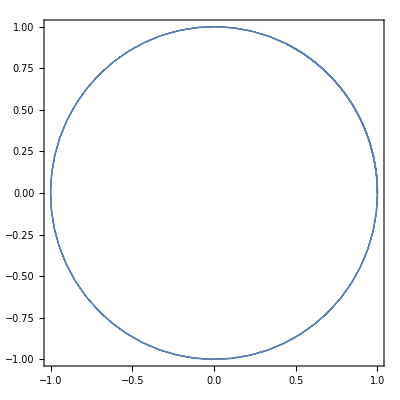

```mathematica
ParametricPlot[
{Cos[θ]/(√(1+4 x^2))+(2 x Sin[θ])/(√(1+4 x^2)),(2 x Cos[θ])/(√(1+4 x^2))-Sin[θ]/(√(1+4 x^2))}
,{x,0,1},{θ,0,2π}]
```

```mathematica
{Cos[θ]/(√(1+4 x^2))+(2 x Sin[θ])/(√(1+4 x^2)),(2 x Cos[θ])/(√(1+4 x^2))-Sin[θ]/(√(1+4 x^2))}/.x->√2
```

{Cos[θ]/3+2/3 √2 Sin[θ],2/3 √2 Cos[θ]-Sin[θ]/3}

```mathematica
{Cos[θ]/(√(1+4 x^2))+(2 x Sin[θ])/(√(1+4 x^2)),(2 x Cos[θ])/(√(1+4 x^2))-Sin[θ]/(√(1+4 x^2))}/.x->1
```

{Cos[θ]/(√5)+(2 Sin[θ])/(√5),(2 Cos[θ])/(√5)-Sin[θ]/(√5)}

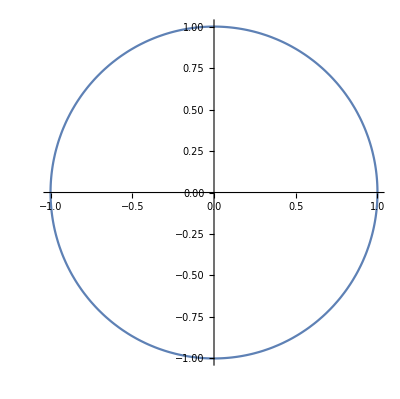

```mathematica
ParametricPlot[
{Cos[θ]/(√5)+(2 Sin[θ])/(√5),(2 Cos[θ])/(√5)-Sin[θ]/(√5)}
,{θ,0,2π}]
```

```mathematica
FullSimplify[
Normalize[D[{x,f[x]},x]].Normalize[{1,1}.RotationMatrix[θ]]
,x∈Reals]
```

(Cos[θ]+Sin[θ]+(Cos[θ]-Sin[θ]) f'[x])/(√2 √((Abs[Cos[θ]]^2+Abs[Sin[θ]]^2) (1+Abs[f'[x]]^2)))

```mathematica
FullSimplify[
Normalize[D[{x,f[x]},x]].Normalize[{1,1}.RotationMatrix[θ]]
,{x,θ,f[x],f'[x]}∈Reals∧0≤θ≤2π]
```

(Cos[θ]+Sin[θ]+(Cos[θ]-Sin[θ]) f'[x])/(√2 √(1+f'[x]^2))

```mathematica
With[{f=Function[x,x^2]},
(Cos[θ]+Sin[θ]+(Cos[θ]-Sin[θ]) f'[x])/(√2 √(1+f'[x]^2))
]
```

(Cos[θ]+2 x (Cos[θ]-Sin[θ])+Sin[θ])/(√2 √(1+4 x^2))

```mathematica
With[{f=Function[x,x^2]},
(Cos[θ]+Sin[θ]+(Cos[θ]-Sin[θ]) f'[x])/(√2 √(1+f'[x]^2))
]
```

(Cos[θ]+2 x (Cos[θ]-Sin[θ])+Sin[θ])/(√2 √(1+4 x^2))

```mathematica
(Cos[θ]+2 x (Cos[θ]-Sin[θ])+Sin[θ])/(√2 √(1+4 x^2))/.x->1
```

(Cos[θ]+2 (Cos[θ]-Sin[θ])+Sin[θ])/(√10)

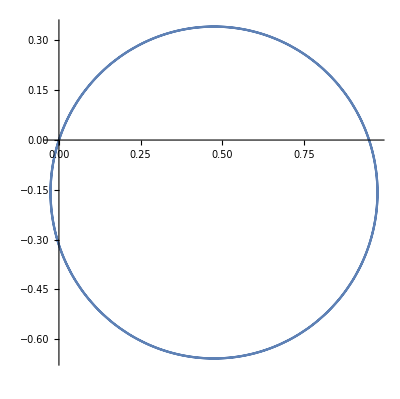

```mathematica
PolarPlot[(Cos[θ]+2 (Cos[θ]-Sin[θ])+Sin[θ])/(√10),{θ,0,2 π}]
```

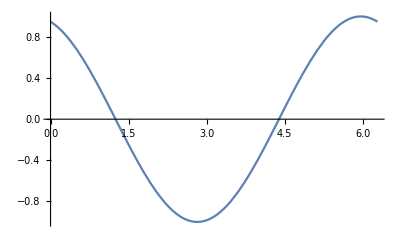

```mathematica
Plot[(Cos[θ]+2 (Cos[θ]-Sin[θ])+Sin[θ])/(√10),{θ,0,2π}]
```

```mathematica
Solve[(Cos[θ]+2 (Cos[θ]-Sin[θ])+Sin[θ])/(√10)==1,θ,Reals]
```

{{θ→ConditionalExpression[-2 ArcTan[1/(3+√10)]+2 π C[1],C[1]∈ℤ]}}

```mathematica
FullSimplify[
Normalize[D[{x,f[x]},x]].Normalize[{1,1}.RotationMatrix[θ]]
,{x,θ,f[x],f'[x]}∈Reals∧0≤θ≤2π]
```

(Cos[θ]+Sin[θ]+(Cos[θ]-Sin[θ]) f'[x])/(√2 √(1+f'[x]^2))

```mathematica
FullSimplify[
Solve[Normalize[D[{x,f[x]},x]].Normalize[{1,1}.RotationMatrix[θ]]==1,θ,Reals]
,{x,θ,f[x],f'[x]}∈Reals∧0≤θ≤2π]
```

Solve[(Cos[θ]+Sin[θ]+(Cos[θ]-Sin[θ]) f'[x])/(√2 √(1+f'[x]^2))==1,θ,ℝ]

```mathematica
Manipulate[
Plot[(Cos[θ]+2 x (Cos[θ]-Sin[θ])+Sin[θ])/(√2 √(1+4 x^2)),{θ,0,2π}]
,{x,0,10}]
```

```mathematica
Plot3D[(Cos[θ]+2 x (Cos[θ]-Sin[θ])+Sin[θ])/(√2 √(1+4 x^2)),{x,-2,2},{θ,0,2π}]
```

-Graphics3D-

```mathematica
Plot3D[(Cos[θ]+2 x (Cos[θ]-Sin[θ])+Sin[θ])/(√2 √(1+4 x^2)),{x,-10,10},{θ,0,2π}]
```

-Graphics3D-

```mathematica
FullSimplify[
Solve[Normalize[D[{x,f[x]},x]].Normalize[{1,1}.RotationMatrix[θ]]==1,θ,Reals]
,{x,θ,f[x],f'[x]}∈Reals∧0≤θ≤2π]
```

Solve[(Cos[θ]+Sin[θ]+(Cos[θ]-Sin[θ]) f'[x])/(√2 √(1+f'[x]^2))==1,θ,ℝ]

```mathematica
Solve[(Cos[θ]+Sin[θ]+(Cos[θ]-Sin[θ]) f'[x])/(√2 √(1+f'[x]^2))==1/.f->Identity,θ,Reals]
```

{{θ→ConditionalExpression[2 π C[1],C[1]∈ℤ]}}

```mathematica
Plot3D[(Cos[θ]+2 x (Cos[θ]-Sin[θ])+Sin[θ])/(√2 √(1+4 x^2)),{x,-10,10},{θ,0,2π},PlotRange->{-1,1}]
```

-Graphics3D-

```mathematica
((Cos[θ]+Sin[θ]+(Cos[θ]-Sin[θ]) f'[x])/(√2 √(1+f'[x]^2)))^2
```

(Cos[θ]+Sin[θ]+(Cos[θ]-Sin[θ]) f'[x])^2/(2 (1+f'[x]^2))

```mathematica
TrigReduce[(Cos[θ]+Sin[θ]+(Cos[θ]-Sin[θ]) f'[x])^2/(2 (1+f'[x]^2))]
```

(1+Sin[2 θ]+2 Cos[2 θ] f'[x]+f'[x]^2-Sin[2 θ] f'[x]^2)/(2 (1+f'[x]^2))

```mathematica
√((1+Sin[2 θ]+2 Cos[2 θ] f'[x]+f'[x]^2-Sin[2 θ] f'[x]^2)/(2 (1+f'[x]^2)))
```

(√((1+Sin[2 θ]+2 Cos[2 θ] f'[x]+f'[x]^2-Sin[2 θ] f'[x]^2)/(1+f'[x]^2)))/(√2)